```mathematica
<<MaTeX`
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<Teukolsky`
```

```mathematica
Get["../../SpinningTrajectory.wl"]
```

```mathematica
Get["../../TeukolskySpinFluxes.wl"]
```

## Calculation

### Trajectory

Set orbital parameters

```mathematica
s=0.01`48;
```

```mathematica
lists={-2,-1,1,2}*s;
```

```mathematica
a=0.9`64
p=12.0`64
e=0.2`64
x=0.5`64
```

0.9

12.

0.2

0.5

Calculate numerical corrections

```mathematica
AbsoluteTiming[corr8=KerrSpinOrbitCorrection[a,p,e,x,8,8];]
```

Calculating t, ϕ equations

Calculating r equation

Calculating θ equation

Calculating norm equation

Calculating submatrices

Calculating v

Calculating ES,LS

Calculating UtSlist, UϕSlist

Calculating Uthatlist, Uϕhatlist

Calculating UtSfour, UϕSfour

Calculating Uthatfour, Uϕhatfour

Calculating ImΔtSfour, ImΔϕSfour

{13.5356,Null}

```mathematica
corr8["error"]
```

5.628732676755007023647521×10^-6

```mathematica
AbsoluteTiming[corr16=KerrSpinOrbitCorrection[a,p,e,x,8,16];]
```

Calculating t, ϕ equations

Calculating r equation

Calculating θ equation

Calculating norm equation

Calculating submatrices

Calculating v

Calculating ES,LS

Calculating UtSlist, UϕSlist

Calculating Uthatlist, Uϕhatlist

Calculating UtSfour, UϕSfour

Calculating Uthatfour, Uϕhatfour

Calculating ImΔtSfour, ImΔϕSfour

{40.47,Null}

```mathematica
corr16["error"]
```

6.89517916046983×10^-8

Calculate analytical trajectories

```mathematica
orbits=Table[KerrSpinOrbit[SetPrecision[a,32],SetPrecision[p,32],SetPrecision[e,32],SetPrecision[x,32],lists[[i]],"Gauge"->"pex"],{i,1,4}];
```

### Fluxes

Mode numbers

```mathematica
l=2
m=2
n=0
```

2

2

0

Calculate Teukolsky amplitudes for different spins and k indices

```mathematica
modes8=Table[Table[TeukolskySpinModeFromCorrection[l,m,n,k,corr8,lists[[i]]],{k,-10,10}],{i,1,4}];
```

160 steps in wr, 416 steps in wθ

128 steps in wr, 384 steps in wθ

128 steps in wr, 352 steps in wθ

96 steps in wr, 320 steps in wθ

96 steps in wr, 288 steps in wθ

64 steps in wr, 256 steps in wθ

64 steps in wr, 224 steps in wθ

32 steps in wr, 160 steps in wθ

32 steps in wr, 128 steps in wθ

32 steps in wr, 96 steps in wθ

64 steps in wr, 64 steps in wθ

64 steps in wr, 64 steps in wθ

96 steps in wr, 96 steps in wθ

96 steps in wr, 128 steps in wθ

128 steps in wr, 160 steps in wθ

128 steps in wr, 192 steps in wθ

160 steps in wr, 224 steps in wθ

160 steps in wr, 256 steps in wθ

192 steps in wr, 288 steps in wθ

224 steps in wr, 320 steps in wθ

224 steps in wr, 352 steps in wθ

160 steps in wr, 416 steps in wθ

128 steps in wr, 384 steps in wθ

128 steps in wr, 352 steps in wθ

96 steps in wr, 320 steps in wθ

96 steps in wr, 288 steps in wθ

64 steps in wr, 256 steps in wθ

64 steps in wr, 224 steps in wθ

32 steps in wr, 160 steps in wθ

32 steps in wr, 128 steps in wθ

32 steps in wr, 96 steps in wθ

64 steps in wr, 64 steps in wθ

64 steps in wr, 64 steps in wθ

96 steps in wr, 96 steps in wθ

96 steps in wr, 128 steps in wθ

128 steps in wr, 160 steps in wθ

128 steps in wr, 192 steps in wθ

160 steps in wr, 224 steps in wθ

160 steps in wr, 256 steps in wθ

192 steps in wr, 288 steps in wθ

224 steps in wr, 320 steps in wθ

224 steps in wr, 352 steps in wθ

160 steps in wr, 416 steps in wθ

128 steps in wr, 384 steps in wθ

128 steps in wr, 352 steps in wθ

96 steps in wr, 320 steps in wθ

96 steps in wr, 288 steps in wθ

64 steps in wr, 256 steps in wθ

64 steps in wr, 224 steps in wθ

32 steps in wr, 160 steps in wθ

32 steps in wr, 128 steps in wθ

32 steps in wr, 96 steps in wθ

64 steps in wr, 64 steps in wθ

64 steps in wr, 64 steps in wθ

96 steps in wr, 96 steps in wθ

96 steps in wr, 128 steps in wθ

128 steps in wr, 160 steps in wθ

128 steps in wr, 192 steps in wθ

160 steps in wr, 224 steps in wθ

160 steps in wr, 256 steps in wθ

192 steps in wr, 288 steps in wθ

224 steps in wr, 320 steps in wθ

224 steps in wr, 352 steps in wθ

160 steps in wr, 416 steps in wθ

128 steps in wr, 384 steps in wθ

128 steps in wr, 352 steps in wθ

96 steps in wr, 320 steps in wθ

96 steps in wr, 288 steps in wθ

64 steps in wr, 256 steps in wθ

64 steps in wr, 224 steps in wθ

32 steps in wr, 160 steps in wθ

32 steps in wr, 128 steps in wθ

32 steps in wr, 96 steps in wθ

64 steps in wr, 64 steps in wθ

64 steps in wr, 64 steps in wθ

96 steps in wr, 96 steps in wθ

96 steps in wr, 128 steps in wθ

128 steps in wr, 160 steps in wθ

128 steps in wr, 192 steps in wθ

160 steps in wr, 224 steps in wθ

160 steps in wr, 256 steps in wθ

192 steps in wr, 288 steps in wθ

224 steps in wr, 320 steps in wθ

224 steps in wr, 352 steps in wθ

```mathematica
modes16=Table[Table[TeukolskySpinModeFromCorrection[l,m,n,k,corr16,lists[[i]]],{k,-10,10}],{i,1,4}];
```

160 steps in wr, 416 steps in wθ

128 steps in wr, 384 steps in wθ

128 steps in wr, 352 steps in wθ

96 steps in wr, 320 steps in wθ

96 steps in wr, 288 steps in wθ

64 steps in wr, 256 steps in wθ

64 steps in wr, 224 steps in wθ

32 steps in wr, 160 steps in wθ

32 steps in wr, 128 steps in wθ

32 steps in wr, 96 steps in wθ

64 steps in wr, 64 steps in wθ

64 steps in wr, 64 steps in wθ

96 steps in wr, 96 steps in wθ

96 steps in wr, 128 steps in wθ

128 steps in wr, 160 steps in wθ

128 steps in wr, 192 steps in wθ

160 steps in wr, 224 steps in wθ

160 steps in wr, 256 steps in wθ

192 steps in wr, 288 steps in wθ

224 steps in wr, 320 steps in wθ

224 steps in wr, 352 steps in wθ

160 steps in wr, 416 steps in wθ

128 steps in wr, 384 steps in wθ

128 steps in wr, 352 steps in wθ

96 steps in wr, 320 steps in wθ

96 steps in wr, 288 steps in wθ

64 steps in wr, 256 steps in wθ

64 steps in wr, 224 steps in wθ

32 steps in wr, 160 steps in wθ

32 steps in wr, 128 steps in wθ

32 steps in wr, 96 steps in wθ

64 steps in wr, 64 steps in wθ

64 steps in wr, 64 steps in wθ

96 steps in wr, 96 steps in wθ

96 steps in wr, 128 steps in wθ

128 steps in wr, 160 steps in wθ

128 steps in wr, 192 steps in wθ

160 steps in wr, 224 steps in wθ

160 steps in wr, 256 steps in wθ

192 steps in wr, 288 steps in wθ

224 steps in wr, 320 steps in wθ

224 steps in wr, 352 steps in wθ

160 steps in wr, 416 steps in wθ

128 steps in wr, 384 steps in wθ

128 steps in wr, 352 steps in wθ

96 steps in wr, 320 steps in wθ

96 steps in wr, 288 steps in wθ

64 steps in wr, 256 steps in wθ

64 steps in wr, 224 steps in wθ

32 steps in wr, 160 steps in wθ

32 steps in wr, 128 steps in wθ

32 steps in wr, 96 steps in wθ

64 steps in wr, 64 steps in wθ

64 steps in wr, 64 steps in wθ

96 steps in wr, 96 steps in wθ

96 steps in wr, 128 steps in wθ

128 steps in wr, 160 steps in wθ

128 steps in wr, 192 steps in wθ

160 steps in wr, 224 steps in wθ

160 steps in wr, 256 steps in wθ

192 steps in wr, 288 steps in wθ

224 steps in wr, 320 steps in wθ

224 steps in wr, 352 steps in wθ

160 steps in wr, 416 steps in wθ

128 steps in wr, 384 steps in wθ

128 steps in wr, 352 steps in wθ

96 steps in wr, 320 steps in wθ

96 steps in wr, 288 steps in wθ

64 steps in wr, 256 steps in wθ

64 steps in wr, 224 steps in wθ

32 steps in wr, 160 steps in wθ

32 steps in wr, 128 steps in wθ

32 steps in wr, 96 steps in wθ

64 steps in wr, 64 steps in wθ

64 steps in wr, 64 steps in wθ

96 steps in wr, 96 steps in wθ

96 steps in wr, 128 steps in wθ

128 steps in wr, 160 steps in wθ

128 steps in wr, 192 steps in wθ

160 steps in wr, 224 steps in wθ

160 steps in wr, 256 steps in wθ

192 steps in wr, 288 steps in wθ

224 steps in wr, 320 steps in wθ

224 steps in wr, 352 steps in wθ

```mathematica
modesAn=Table[Table[TeukolskySpinModeAnalytical[l,m,n,k,orbits[[i]]],{k,-10,10}],{i,1,4}];
```

160 steps in wr, 416 steps in wz

128 steps in wr, 384 steps in wz

128 steps in wr, 352 steps in wz

96 steps in wr, 320 steps in wz

96 steps in wr, 288 steps in wz

64 steps in wr, 256 steps in wz

64 steps in wr, 192 steps in wz

32 steps in wr, 160 steps in wz

32 steps in wr, 128 steps in wz

32 steps in wr, 96 steps in wz

64 steps in wr, 64 steps in wz

64 steps in wr, 64 steps in wz

96 steps in wr, 96 steps in wz

96 steps in wr, 128 steps in wz

128 steps in wr, 160 steps in wz

128 steps in wr, 192 steps in wz

160 steps in wr, 224 steps in wz

160 steps in wr, 256 steps in wz

192 steps in wr, 288 steps in wz

224 steps in wr, 320 steps in wz

224 steps in wr, 352 steps in wz

160 steps in wr, 416 steps in wz

128 steps in wr, 384 steps in wz

128 steps in wr, 352 steps in wz

96 steps in wr, 320 steps in wz

96 steps in wr, 288 steps in wz

64 steps in wr, 256 steps in wz

64 steps in wr, 192 steps in wz

32 steps in wr, 160 steps in wz

32 steps in wr, 128 steps in wz

32 steps in wr, 96 steps in wz

64 steps in wr, 64 steps in wz

64 steps in wr, 64 steps in wz

96 steps in wr, 96 steps in wz

96 steps in wr, 128 steps in wz

128 steps in wr, 160 steps in wz

128 steps in wr, 192 steps in wz

160 steps in wr, 224 steps in wz

160 steps in wr, 256 steps in wz

192 steps in wr, 288 steps in wz

224 steps in wr, 320 steps in wz

224 steps in wr, 352 steps in wz

160 steps in wr, 416 steps in wz

128 steps in wr, 384 steps in wz

128 steps in wr, 352 steps in wz

96 steps in wr, 320 steps in wz

96 steps in wr, 288 steps in wz

64 steps in wr, 256 steps in wz

64 steps in wr, 224 steps in wz

32 steps in wr, 160 steps in wz

32 steps in wr, 128 steps in wz

32 steps in wr, 96 steps in wz

64 steps in wr, 64 steps in wz

64 steps in wr, 64 steps in wz

96 steps in wr, 96 steps in wz

96 steps in wr, 128 steps in wz

128 steps in wr, 160 steps in wz

128 steps in wr, 192 steps in wz

160 steps in wr, 224 steps in wz

160 steps in wr, 256 steps in wz

192 steps in wr, 288 steps in wz

224 steps in wr, 320 steps in wz

224 steps in wr, 352 steps in wz

160 steps in wr, 416 steps in wz

128 steps in wr, 384 steps in wz

128 steps in wr, 352 steps in wz

96 steps in wr, 320 steps in wz

96 steps in wr, 288 steps in wz

64 steps in wr, 256 steps in wz

64 steps in wr, 224 steps in wz

32 steps in wr, 160 steps in wz

32 steps in wr, 128 steps in wz

32 steps in wr, 96 steps in wz

64 steps in wr, 64 steps in wz

64 steps in wr, 64 steps in wz

96 steps in wr, 96 steps in wz

96 steps in wr, 128 steps in wz

128 steps in wr, 160 steps in wz

128 steps in wr, 192 steps in wz

160 steps in wr, 224 steps in wz

160 steps in wr, 256 steps in wz

192 steps in wr, 288 steps in wz

224 steps in wr, 320 steps in wz

224 steps in wr, 352 steps in wz

Save outputs

```mathematica
Save["modes_results.m",{modes8,modes16,modesAn}]
```

## Plots

Plot numerically calculated linear parts of the amplitudes

```mathematica
pad={{55,Automatic},{Automatic,Automatic}};
```

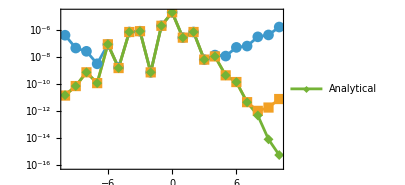

```mathematica
plotC1=ListLogPlot[{Table[{modes8[[1,ik]]["k"],Abs[Table[modes8[[i,ik]]["Amplitudes"]["ℐ"],{i,1,4}].{1/12,-2/3,2/3,-1/12}/s]},{ik,1,Length[modes8[[1]]]}],
Table[{modes16[[1,ik]]["k"],Abs[Table[modes16[[i,ik]]["Amplitudes"]["ℐ"],{i,1,4}].{1/12,-2/3,2/3,-1/12}/s]},{ik,1,Length[modes16[[1]]]}],
Table[{modesAn[[1,ik]]["k"],Abs[Table[modesAn[[i,ik]]["Amplitudes"]["ℐ"],{i,1,4}].{1/12,-2/3,2/3,-1/12}/s]},{ik,1,Length[modesAn[[1]]]}]},Joined->True,PlotMarkers->Automatic,Frame->True,Axes->False,FrameLabel->{None,MaTeX@"| C^{+,1}_{220k} |"},PlotLegends->Placed[{MaTeX@"k^s_{\\max} = 8",MaTeX@"k^s_{\\max} = 16","Analytical"},{0.5,0.3}],FrameStyle->Black,ImageSize->300,ImagePadding->pad]
```

Plot numerically calculated linear parts of the fluxes

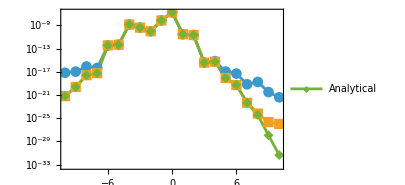

```mathematica
plotF1=ListLogPlot[{Table[{modes8[[1,n]]["k"],Abs[Table[modes8[[i,n]]["Fluxes"]["Energy"]["ℐ"]+modes8[[i,n]]["Fluxes"]["Energy"]["ℋ"],{i,1,4}].{1/12,-2/3,2/3,-1/12}/s]},{n,1,Length[modes8[[1]]]}],
Table[{modes16[[1,n]]["k"],Abs[Table[modes16[[i,n]]["Fluxes"]["Energy"]["ℐ"]+modes16[[i,n]]["Fluxes"]["Energy"]["ℋ"],{i,1,4}].{1/12,-2/3,2/3,-1/12}/s]},{n,1,Length[modes16[[1]]]}],
Table[{modesAn[[1,n]]["k"],Abs[Table[modesAn[[i,n]]["Fluxes"]["Energy"]["ℐ"]+modesAn[[i,n]]["Fluxes"]["Energy"]["ℋ"],{i,1,4}].{1/12,-2/3,2/3,-1/12}/s]},{n,1,Length[modesAn[[1]]]}]},Joined->True,PlotMarkers->Automatic,Frame->True,Axes->False,FrameLabel->MaTeX@{"k","| \\mathcal{F}^{E,1}_{220k} |"},PlotLegends->Placed[{MaTeX@"k^s_{\\max} = 8",MaTeX@"k^s_{\\max} = 16","Analytical"},{0.5,0.3}],FrameStyle->Black,ImageSize->300,ImagePadding->pad]
```

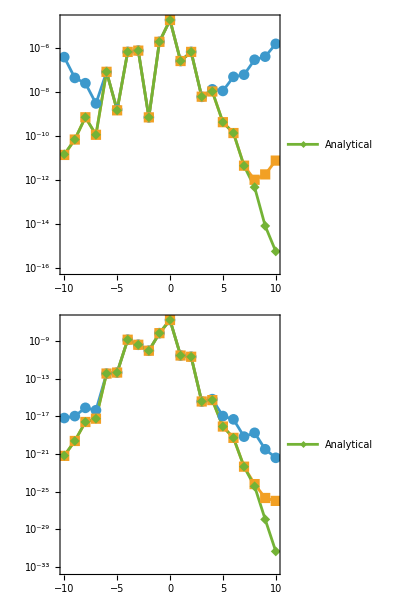

```mathematica
Column[{plotC1,plotF1}]
```

Plot absolute differences between the linear parts of the fluxes

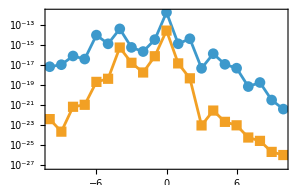

```mathematica
plotabs=ListLogPlot[
{Table[{modes8[[1,n]]["k"],Abs[Table[modes8[[i,n]]["Fluxes"]["Energy"]//Total,{i,1,4}].{1/12,-2/3,2/3,-1/12}/s-Table[modesAn[[i,n]]["Fluxes"]["Energy"]//Total,{i,1,4}].{1/12,-2/3,2/3,-1/12}/s]},{n,1,Length[modes8[[1]]]}],
Table[{modes16[[1,n]]["k"],Abs[Table[modes16[[i,n]]["Fluxes"]["Energy"]//Total,{i,1,4}].{1/12,-2/3,2/3,-1/12}/s-Table[modesAn[[i,n]]["Fluxes"]["Energy"]//Total,{i,1,4}].{1/12,-2/3,2/3,-1/12}/s]},{n,1,Length[modes16[[1]]]}]},
Joined->True,
PlotMarkers->Automatic,
Frame->True,
Axes->False,
FrameLabel->{None,MaTeX@"\\Delta \\mathcal{F}^{E,1}_{220k}"},
PlotLegends->Placed[MaTeX@{"k^s_{\\max} = 8","k^s_{\\max} = 16"},{0.45,0.2}],
FrameStyle->Black,
ImageSize->300,
ImagePadding->pad]
```

Plot relative differences between the linear parts of the fluxes

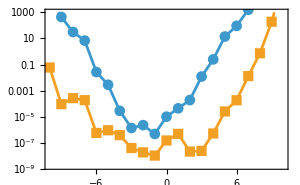

```mathematica
plotrel=ListLogPlot[
{Table[{modes8[[1,n]]["k"],Abs[1-(Table[modes8[[i,n]]["Fluxes"]["Energy"]//Total,{i,1,4}].{1/12,-2/3,2/3,-1/12}/s)/(Table[modesAn[[i,n]]["Fluxes"]["Energy"]//Total,{i,1,4}].{1/12,-2/3,2/3,-1/12}/s)]},{n,1,Length[modes8[[1]]]}],
Table[{modes16[[1,n]]["k"],Abs[1-(Table[modes16[[i,n]]["Fluxes"]["Energy"]//Total,{i,1,4}].{1/12,-2/3,2/3,-1/12}/s)/(Table[modesAn[[i,n]]["Fluxes"]["Energy"]//Total,{i,1,4}].{1/12,-2/3,2/3,-1/12}/s)]},{n,1,Length[modes16[[1]]]}]},
Joined->True,
PlotRange->{Automatic,{All,10^3}},
PlotMarkers->Automatic,
Frame->True,
Axes->False,
FrameLabel->MaTeX@{"k","\\delta \\mathcal{F}^{E,1}_{220k}"},
PlotLegends->Placed[MaTeX@{"k^s_{\\max} = 8","k^s_{\\max} = 16"},{0.45,0.8}],
FrameStyle->Black,
ImageSize->300,
ImagePadding->pad]
```

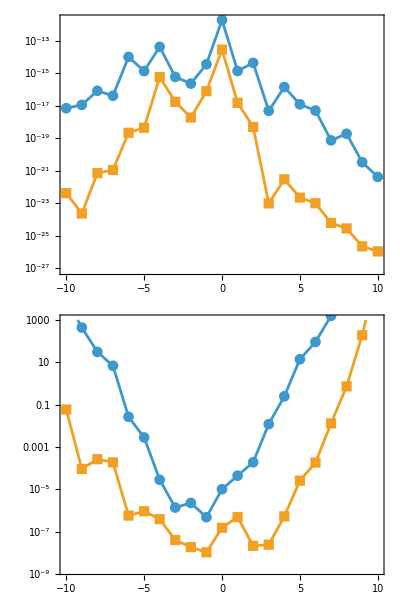

```mathematica
Column[{plotabs,plotrel}]
```